## Bifurcation Diagram Functionality

```mathematica
Clear[peaks,data,ts,runs]
mg[td_,gain_]:=Module[{tdelay=td,init={x[0]==0.5},pars={β->gain,γ->1,n->9.65}},
eq={x'[t]==(β x[t-tdelay])/(1+x[t-tdelay]^n)-γ x[t]};
NDSolveValue[{eq/.pars,init},{x},{t,0,100}]
]
roundPeaks[ts_,tolerance_]:=Module[{},
Table[Round[ts[[i]],tolerance],{i,1,Length@ts}]//DeleteDuplicates
]
coarsePeakQ[ts_,j_,g_]:=Module[{},
If[(AllTrue[Table[ts[[k]],{k,j-g,j-1}],#<ts[[j]]&]&&AllTrue[Table[ts[[k]],{k,j+1,j+g}],#<ts[[j]]&])||(AllTrue[Table[ts[[k]],{k,j-g,j-1}],#>ts[[j]]&]&&AllTrue[Table[ts[[k]],{k,j+1,j+g}],#>ts[[j]]&]),ts[[j]],0]
]
getPeaks[data_,tolerance_:0.02,granularity_:1]:=Module[{ts=If[ListQ[data],data,Table[data[x],{x,0,100,0.1}]],peaks={}},
Monitor[For[i=3,i<Length@ts-3,i++,
AppendTo[peaks,coarsePeakQ[ts,i,granularity]]
],i];
roundPeaks[peaks//DeleteCases[0],tolerance]
]
bifurcationDataG[startG_,endG_,inc_]:=Module[{runs=Table[{i,mg[2,i][[1]]},{i,startG,endG,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{(n+startG-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
bifurcationDataTd[startTd_,endTd_,inc_]:=Module[{runs=Table[{i,mg[i,2][[1]]},{i,startTd,endTd,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{(n+startTd-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
Clear[peaks,data,ts,fixedData]
importData[basePath_]:=Module[{files=FileNames["*.csv",basePath]},
Import[#]&/@files
]
fixData[csv_]:=Module[{},
Table[csv[[j,5]],{j,1,Length@csv}]
]
realBifurcationData[fixedData_,gains_,tolerance_,granularity_]:=Module[{},
peaks=Table[getPeaks[fixedData[[i]],tolerance,granularity],{i,1,Length@fixedData}];
Flatten[Table[Table[{gains[[n]],peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
```

## Lab Waveforms

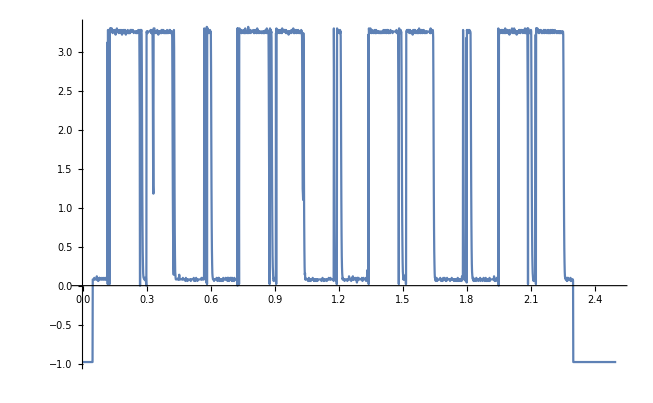

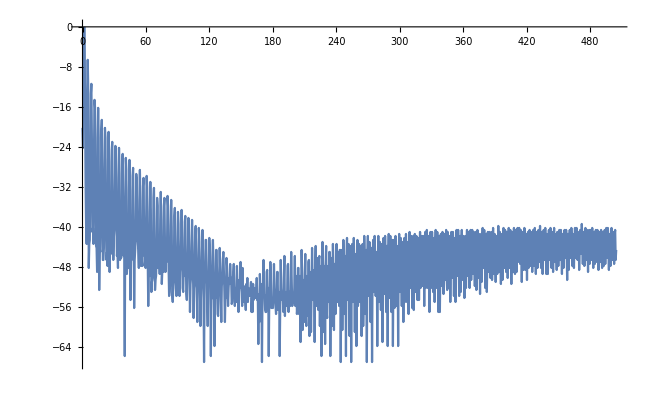

```mathematica
fft=Import["D:\\F20\\Nonlinear Optoelectronic Dynamics\\Week 7\\oeo_300d_33950g_fft.csv","CSV"];
waveform=Import["D:\\F20\\Nonlinear Optoelectronic Dynamics\\Week 7\\BifurcationData\\oeo_300d_33950g.csv","CSV"];
ListPlot[Table[{waveform[[i,4]],waveform[[i,5]]},{i,1,Length@waveform}],Joined->True]
ListPlot[Table[{fft[[i,4]],fft[[i,5]]},{i,1,Length@fft}],Joined->True]
```

```mathematica
waveforms=importData["D:\\F20\\Nonlinear Optoelectronic Dynamics\\Week 7\\BifurcationData\\"];
```

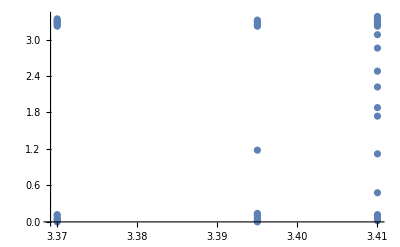

```mathematica
ListPlot[realBifurcationData[fixData[#]&/@waveforms,{3.37,3.395,3.41},0.02,5]]//Quiet
```

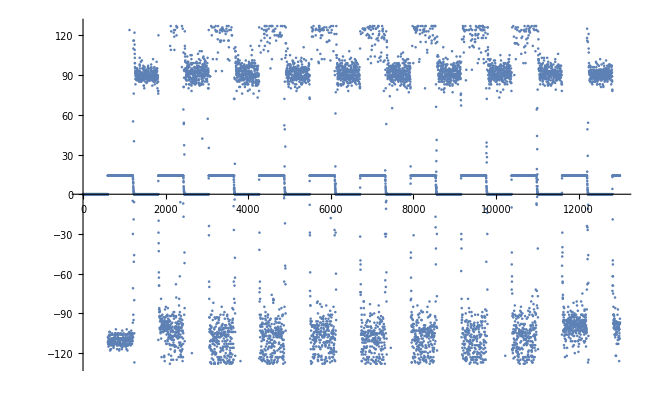

```mathematica
data=BinaryReadList["D:\\F20\\Nonlinear Optoelectronic Dynamics\\Week 7\\data2.bin","Integer8"];
ListPlot[data]
```

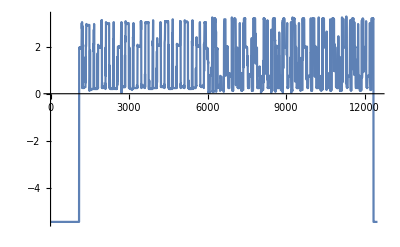

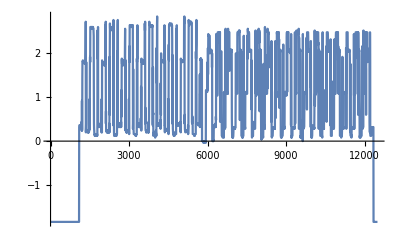

```mathematica
coupledData=Import["C:\\Users\\ctbus\\Downloads\\coupled_oeo_30000_40000_td300_300_2.csv","CSV"];
coupledData1=Table[{coupledData[[i,4]]*500,coupledData[[i,5]]},{i,1,Length@coupledData}];
coupledData2=Table[{coupledData[[i,10]]*500,coupledData[[i,11]]},{i,1,Length@coupledData}];
ListPlot[coupledData1,Joined->True]
ListPlot[coupledData2,Joined->True]
```

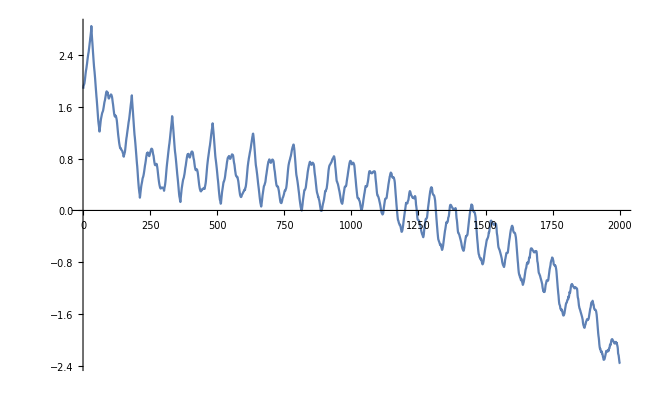

```mathematica
Nx=Min[Length@coupledData1,Length@coupledData2];
x=Table[coupledData1[[i,2]],{i,1,Length@coupledData1}];
y=Table[coupledData2[[i,2]],{i,1,Length@coupledData2}];
Rxy[n_]:=1/(Nx-n) Sum[x[[m]]*y[[m+n]],{m,1,Nx-n}]
ListLinePlot[Table[Rxy[z],{z,0,2000,1}],PlotRange->{All,All}]
```

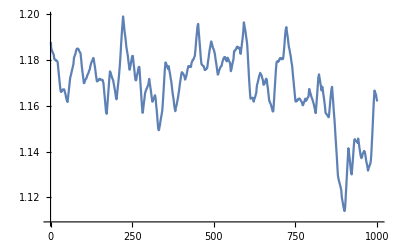

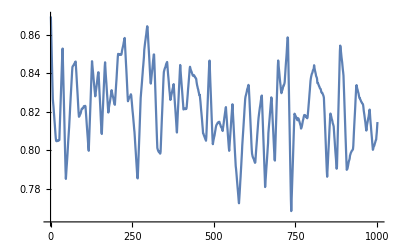

```mathematica
Clear["Global`*"]
getX[coupledData_]:=Module[{coupledData1=Table[{coupledData[[i,4]]*500,coupledData[[i,5]]},{i,1,Length@coupledData}]},
Table[coupledData1[[i,2]],{i,1,Length@coupledData1}]
]
getY[coupledData_]:=Module[{coupledData2=Table[{coupledData[[i,10]]*500,coupledData[[i,11]]},{i,1,Length@coupledData}]},
Table[coupledData2[[i,2]],{i,1,Length@coupledData2}]
]
xCorrFxn[file_]:=Module[{x=getX[Import[file,"CSV"]],y=getY[Import[file,"CSV"]]},
ListLinePlot[Table[1/(Min[Length@x,Length@y]-n) Sum[x[[m]]*y[[m+n]],{m,1,Min[Length@x,Length@y]-n}],{n,0,1000,1}],PlotRange->{All,All}]
]
xCorrMax[file_]:=Module[{x=getX[Import[file,"CSV"]],y=getY[Import[file,"CSV"]]},
Max[Table[1/(Min[Length@x,Length@y]-n) Sum[x[[m]]*y[[m+n]],{m,1,Min[Length@x,Length@y]-n}],{n,0,1000,1}]]
]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.5.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.9.csv"]
```

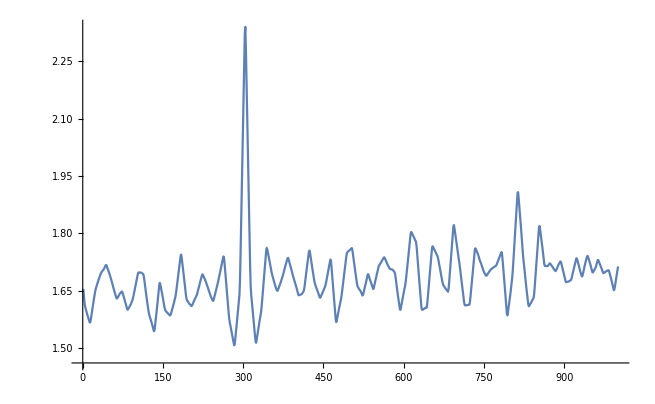

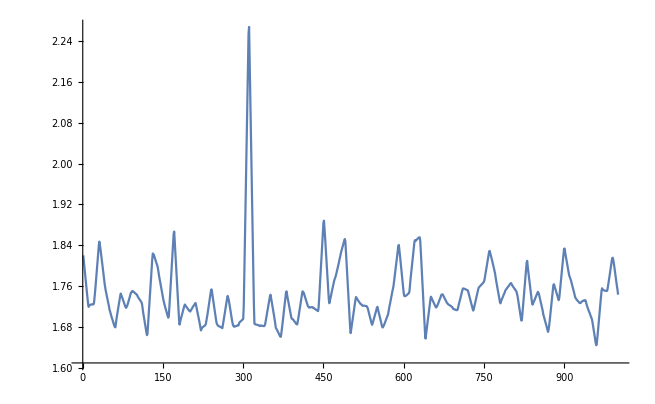

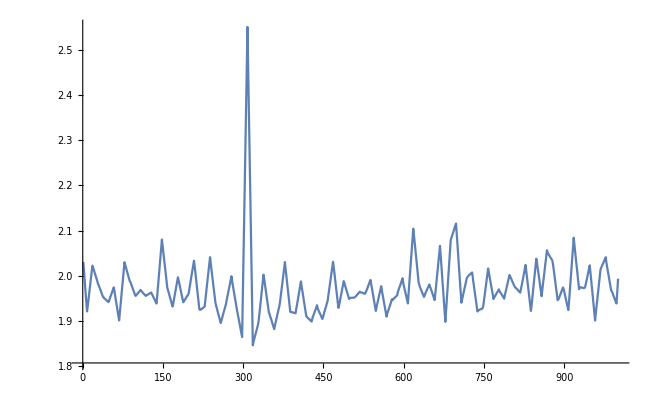

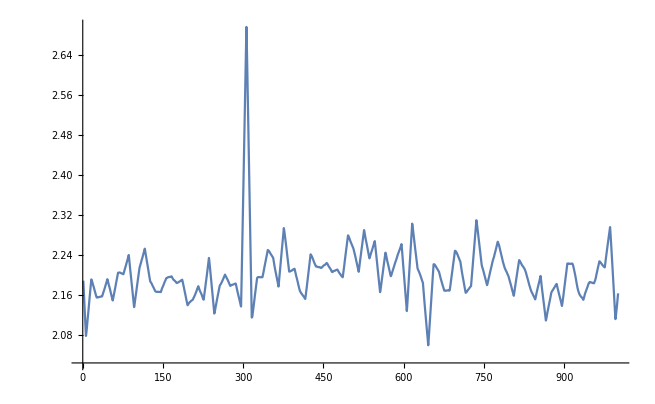

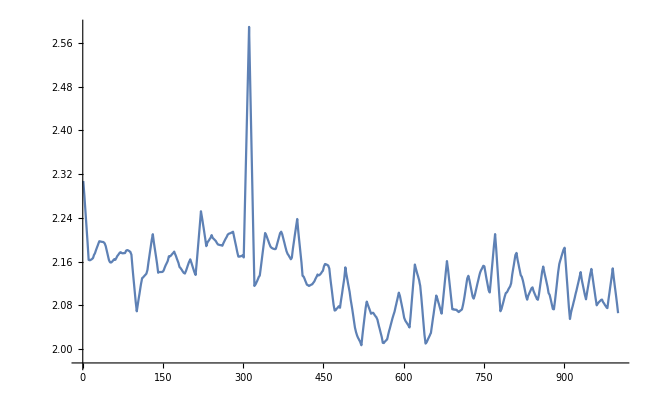

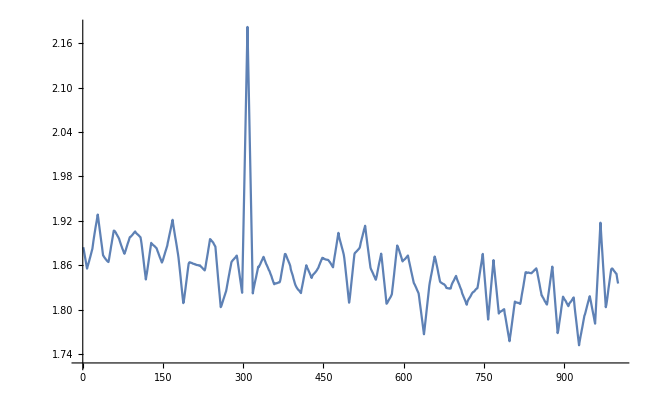

```mathematica
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k1.0_2.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.9_2.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.8_2.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.7_2.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.6_2.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.5_2.csv"]
```

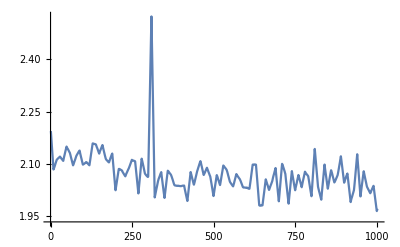

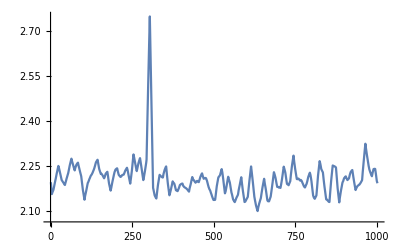

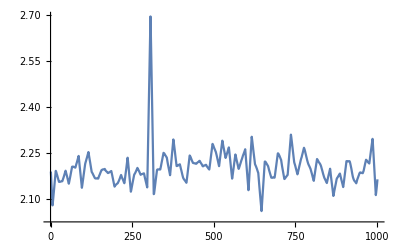

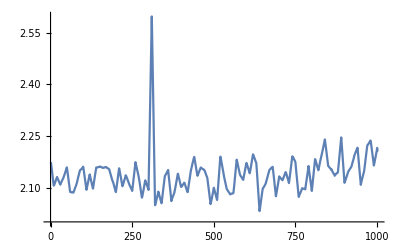

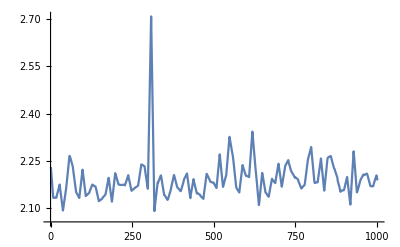

```mathematica
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.68.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.69.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.7_2.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.71.csv"]
xCorrFxn["C:\\Users\\ctbus\\Downloads\\k0.72.csv"]
```

{C:\Users\ctbus\Downloads\k0.5_2.csv,C:\Users\ctbus\Downloads\k0.6_2.csv,C:\Users\ctbus\Downloads\k0.68.csv,C:\Users\ctbus\Downloads\k0.69.csv,C:\Users\ctbus\Downloads\k0.7_2.csv,C:\Users\ctbus\Downloads\k0.71.csv,C:\Users\ctbus\Downloads\k0.72.csv,C:\Users\ctbus\Downloads\k0.8_2.csv,C:\Users\ctbus\Downloads\k0.9_2.csv,C:\Users\ctbus\Downloads\k1.0_2.csv}

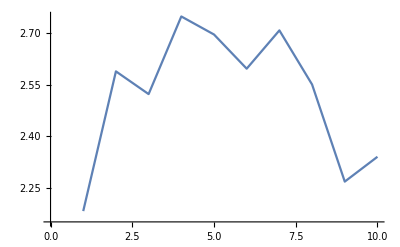

```mathematica
f="C:\\Users\\ctbus\\Downloads\\k"<>#&;
g=#<>".csv"&;
filesOfInterest={"0.5_2","0.6_2","0.68","0.69","0.7_2","0.71","0.72","0.8_2","0.9_2","1.0_2"};filesOfInterest=g/@f/@filesOfInterest
ListPlot[Table[xCorrMax[filesOfInterest[[i]]],{i,1,Length@filesOfInterest}],Joined->True]
```